# Sound Classifier - Math448 - Cameron Embree

```mathematica
(* Set-up to point working directory to pre-recorded audio. Should not need editing. *)
audioDirName="audio/";
nbDir=NotebookDirectory[];
audioPath=nbDir<>audioDirName; 
SetDirectory[audioPath];

Print["Audio dat locatied: ",audioPath,", Working directory set to: ",Directory[]]
```

Audio dat locatied: /Users/csembree/Desktop/sound_classifier/audio/, Working directory set to: /Users/csembree/Desktop/sound_classifier/audio

```mathematica
(* Sound testing *)
```

```mathematica
filterLevel=10000; (* Filter level of 10000 chosen to put collected data into human hearing range *)
Print["Filter Level: ",filterLevel]

idDat={"0","1","2","3","4","5"}; (* Hardcoded strings for each audio sample, used later for generic printing *)
Print["Data File String IDs: ",idDat]

Print["AUDIO FOR ZEROS: "]
loc="0-zero1.wav"
aZero1=Import[loc]
aZeroDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel]
loc="0-zero2.wav"
aZeroDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="0-zero3.wav"
aZeroDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="0-zero4.wav"
aZeroDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="0-zero5.wav"
aZeroDat5=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="0-zero6.wav"
aZeroDat6=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["AUDIO FOR ONES: "]
loc="1-one1.wav"
aOneDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="1-one2.wav"
aOneDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="1-one3.wav"
aOneDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="1-one4.wav"
aOneDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="1-one5.wav"
aOneDat5=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="1-one6.wav"
aOneDat6=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["AUDIO FOR TWOS: "]
loc="2-two1.wav"
aTwoDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="2-two2.wav"
aTwoDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="2-two3.wav"
aTwoDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="2-two4.wav"
aTwoDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="2-two5.wav"
aTwoDat5=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="2-two6.wav"
aTwoDat6=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["AUDIO FOR THREES: "]
loc="3-three1.wav"
aThreeDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="3-three2.wav"
aThreeDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="3-three3.wav"
aThreeDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="3-three4.wav"
aThreeDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="3-three5.wav"
aThreeDat5=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="3-three6.wav"
aThreeDat6=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["AUDIO FOR FOURS: "]
loc="4-four1.wav"
aFourDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="4-four2.wav"
aFourDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="4-four3.wav"
aFourDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="4-four4.wav"
aFourDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="4-four5.wav"
aFourDat5=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="4-four6.wav"
aFourDat6=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

Print["AUDIO FOR FIVE: "]
loc="5-five1.wav"
aFiveDat1=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="5-five2.wav"
aFiveDat2=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="5-five3.wav"
aFiveDat3=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="5-five4.wav"
aFiveDat4=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="5-five5.wav"
aFiveDat5=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];
loc="5-five6.wav"
aFiveDat6=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

(* raw audio data in NxN matrix, where N is the number of different words in the word bank *)
aDat={{aZeroDat1,aZeroDat2,aZeroDat3,aZeroDat4,aZeroDat5,aZeroDat6},
{aOneDat1,aOneDat2,aOneDat3,aOneDat4,aOneDat5,aOneDat6},
{aTwoDat1,aTwoDat2,aTwoDat3,aTwoDat4,aTwoDat5,aTwoDat6},
{aThreeDat1,aThreeDat2,aThreeDat3,aThreeDat4,aThreeDat5,aThreeDat6},
{aFourDat1,aFourDat2,aFourDat3,aFourDat4,aFourDat5,aFourDat6},
{aFiveDat1,aFiveDat2,aFiveDat3,aFiveDat4,aFiveDat5,aFiveDat6}};
```

Filter Level: 10000

Data File String IDs: {0,1,2,3,4,5}

AUDIO FOR ZEROS:

0-zero1.wav

-Graphics-

SampledSoundList[{{-0.000491879,-0.000418464,-0.000555691,-0.000630011,-0.000491213,-0.00062828,-0.00070707,-0.000697935,-0.000662084,-0.000537628,-0.000597015,-0.000687412,«88177»,0.00174137,0.00185249,0.00181379,0.00168674,0.00174489,0.00162073,0.00174034,0.00173647,0.00176234,0.00169545,0.00178128},{«1»}},44100]

0-zero2.wav

0-zero3.wav

0-zero4.wav

0-zero5.wav

0-zero6.wav

AUDIO FOR ONES:

1-one1.wav

1-one2.wav

1-one3.wav

1-one4.wav

1-one5.wav

1-one6.wav

AUDIO FOR TWOS:

2-two1.wav

2-two2.wav

2-two3.wav

2-two4.wav

2-two5.wav

2-two6.wav

AUDIO FOR THREES:

3-three1.wav

3-three2.wav

3-three3.wav

3-three4.wav

3-three5.wav

3-three6.wav

AUDIO FOR FOURS:

4-four1.wav

4-four2.wav

4-four3.wav

4-four4.wav

4-four5.wav

4-four6.wav

AUDIO FOR FIVE:

5-five1.wav

5-five2.wav

5-five3.wav

5-five4.wav

5-five5.wav

5-five6.wav

```mathematica
(* Compute the Fourier discrete cosine transform of each audio sample *)
aDatFTs=Table[Abs[FourierDCT[aDat[[i,j,1,1]]]],{i,1,aDat//Length},{j,1,aDat[[i]]//Length}];

(* Remove the parts of each sample above 10,000 threshold *)
aDatFTs=Table[aDatFTs[[i,j]][[;;filterLevel]],{i,1,aDat//Length},{j,1,aDat[[1]]//Length}] ;
```

Data for sounds in form {{zero},{one},{two},{three},{four},{five}}:

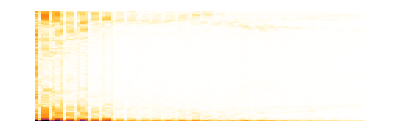
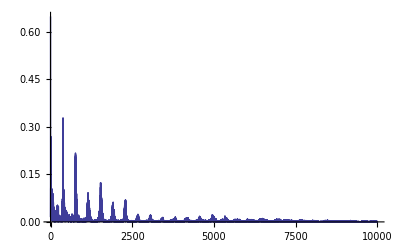
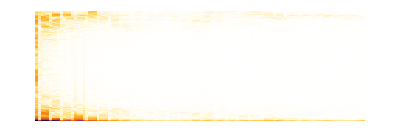
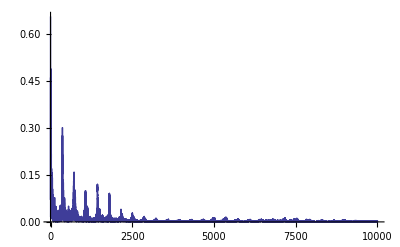
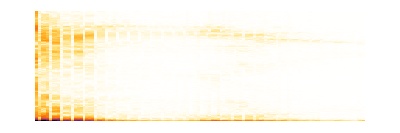
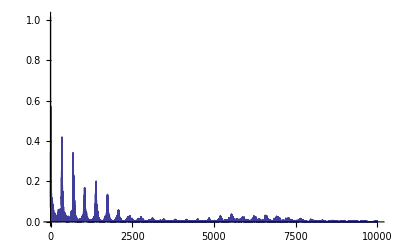
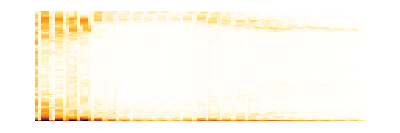
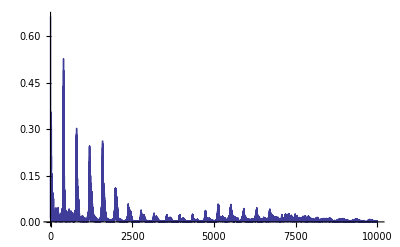

```mathematica
(* Print the Spectrogram and raw Foruier Transofrm data to visually note how each word looks *)
(* this is a N by N matrix, so each N elements represent the Fourier data for one word in the word bank *)
FourierAndSpec[dat_]:=Module[{},
{Spectrogram[dat],ListLinePlot[dat,PlotRange->All]} (* Just for convenience of calling *)
]

(* visual of FTs across all samples *)
res=Table[FourierAndSpec[aDatFTs[[i,j]]],{i,1,aDat//Length},{j,1,aDat[[i]]//Length}];

(* visual of FTs across all samples *)
Print["Data for sounds in form {{zero},{one},{two},{three},{four},{five}}: "]
res=Table[res[[i,j]],{i,1,aDat//Length},{j,1,aDat[[i]]//Length}]
```

Data for avg sounds in form {{zero},{one},{two},{three},{four},{five}}:

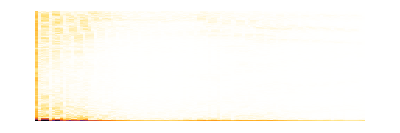
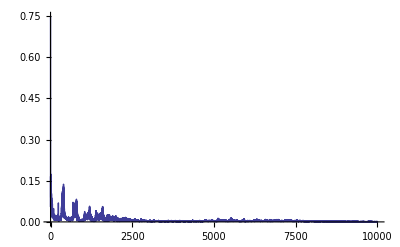
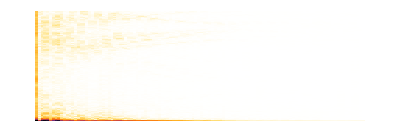
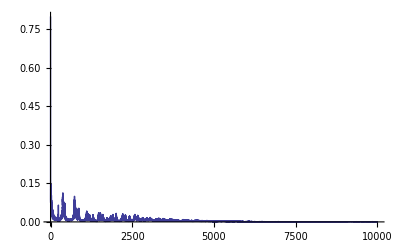
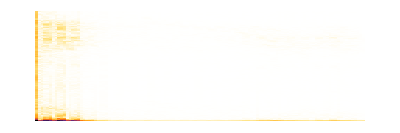
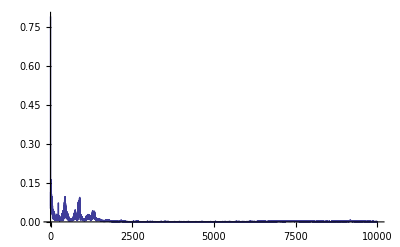
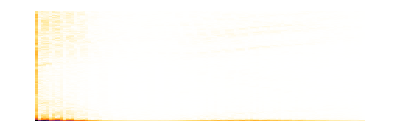
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(* Compute the average Fourier Transofrm by each set of Fourier Transforms *)

avgFT[FTset_]:=Module[{numSamples=0,numDataPoints=0,allAtPos=0,localAvgFT=0},
numSamples=FTset//Length; (* Num of FT data *)
numDataPoints=FTset[[1]]//Length; (* NUM of FT Data*)
(*Print["numSamples: ", numSamples,", numDataPoints: ",numDataPoints];*)
allAtPos=Table[FTset[[j,k]],{k,1,numDataPoints},{j,1,numSamples}];
localAvgFT=Table[Total[allAtPos[[i]]]/numSamples,{i,1,numDataPoints}]
]

(* create avg FT across samples *)
aDatFTavg=Table[avgFT[aDatFTs[[i]]],{i,1,aDat//Length}]; 

(* visual of avg FTs *)
Print["Data for avg sounds in form {{zero},{one},{two},{three},{four},{five}}: "]
res=Table[{Spectrogram[aDatFTavg[[i]]],ListLinePlot[aDatFTavg[[i]],PlotRange->All]},{i,1,aDatFTavg//Length}]
```

```mathematica
getFit[dat_]:=Module[{},
model=aa*Cos[x/500]+bb*Cos[x/1000]+cc*Cos[x/1500]+dd*Cos[x/2000]+ee*Cos[x/2500]+ff*Cos[x/3000]+gg*Cos[x/3500]+hh*Cos[x/4000]+ii*Cos[x/4500]+jj*Cos[x/5000]+kk*Cos[x/5500]+ll*Cos[x/6000]+mm*Cos[x/6500]+nn*Cos[x/7000]+oo*Cos[x/7500]+pp*Cos[x/8000]+qq*Cos[x/8500]+rr*Cos[x/9000]+ss*Cos[x/9500]+tt*Cos[x/10000];
variables={aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt};
nf=FindFit[dat,model,variables,x,MaxIterations->1000];
mod=model/.nf
]

(* Attempt to get fit using scalar multiples of combinations of periodic functions with differing periods *)
 (* Get the fits with periodic functions *)
fs=Table[getFit[aDatFTavg[[i]]],{i,1,aDat//Length}]
 (* Overlay of best-fits for visual comparisions*)
Plot[Tooltip[fs,idDat],{x,0,filterLevel},PlotLegends->idDat]
(* individual overlays of frequencies and best-fits *)
Table[ListLinePlot[{aDatFTavg[[i]],Table[fs[[i]],{x,0,filterLevel}]},PlotStyle->{Thickness[0.015]}],{i,1,fits//Length}] 

(* Best fits to Fourier Transform data using polynomail of form in "accuracyPoly" *)
accuracyPoly={1,x,x^2,x^3,x^3,x^4,x^5,x^6} (* Lower and higher degree polynomials performed worse *)
 (* Best fits using 6th degree polynomial *)
fits=Table[Fit[aDatFTavg[[i]],accuracyPoly,x],{i,1,aDatFTavg//Length}]
(* Overlay of best-fits for visual comparisions *)
Plot[Tooltip[fits,idDat],{x,0,filterLevel},PlotLegends->idDat] 
(* individual overlays of frequencies and best-fits *)
Table[ListLinePlot[{aDatFTavg[[i]],Table[fits[[i]],{x,0,filterLevel}]},PlotStyle->{Thickness[0.015]}],{i,1,fits//Length}]
```

{7.89159×10^8 Cos[x/10000]+3.27756×10^8 Cos[x/9500]-8.9012×10^7 Cos[x/9000]-4.27085×10^8 Cos[x/8500]-6.41003×10^8 Cos[x/8000]-6.76097×10^8 Cos[x/7500]-4.78754×10^8 Cos[x/7000]-2.79599×10^7 Cos[x/6500]+5.92514×10^8 Cos[x/6000]+1.06756×10^9 Cos[x/5500]+7.80583×10^8 Cos[x/5000]-6.76788×10^8 Cos[x/4500]-1.655×10^9 Cos[x/4000]+1.48984×10^9 Cos[x/3500]-4.18834×10^8 Cos[x/3000]+4.472×10^7 Cos[x/2500]-1.61511×10^6 Cos[x/2000]+14023.4 Cos[x/1500]-14.4399 Cos[x/1000]+0.00303921 Cos[x/500],1.18059×10^9 Cos[x/10000]+4.90256×10^8 Cos[x/9500]-1.33277×10^8 Cos[x/9000]-6.3905×10^8 Cos[x/8500]-9.59039×10^8 Cos[x/8000]-1.01145×10^9 Cos[x/7500]-7.16088×10^8 Cos[x/7000]-4.15288×10^7 Cos[x/6500]+8.86823×10^8 Cos[x/6000]+1.59741×10^9 Cos[x/5500]+1.16759×10^9 Cos[x/5000]-1.0134×10^9 Cos[x/4500]-2.4766×10^9 Cos[x/4000]+2.23053×10^9 Cos[x/3500]-6.27403×10^8 Cos[x/3000]+6.70467×10^7 Cos[x/2500]-2.42528×10^6 Cos[x/2000]+21132.5 Cos[x/1500]-22.032 Cos[x/1000]+0.00571039 Cos[x/500],4.09275×10^8 Cos[x/10000]+1.70086×10^8 Cos[x/9500]-4.59903×10^7 Cos[x/9000]-2.21305×10^8 Cos[x/8500]-3.32297×10^8 Cos[x/8000]-3.50628×10^8 Cos[x/7500]-2.48493×10^8 Cos[x/7000]-1.49549×10^7 Cos[x/6500]+3.06659×10^8 Cos[x/6000]+5.53171×10^8 Cos[x/5500]+4.05086×10^8 Cos[x/5000]-3.49597×10^8 Cos[x/4500]-8.57264×10^8 Cos[x/4000]+7.70051×10^8 Cos[x/3500]-2.15951×10^8 Cos[x/3000]+2.29676×10^7 Cos[x/2500]-823343. Cos[x/2000]+7020.58 Cos[x/1500]-6.68394 Cos[x/1000]+0.00259287 Cos[x/500],1.16183×10^9 Cos[x/10000]+4.8252×10^8 Cos[x/9500]-1.31071×10^8 Cos[x/9000]-6.28799×10^8 Cos[x/8500]-9.4373×10^8 Cos[x/8000]-9.95379×10^8 Cos[x/7500]-7.04813×10^8 Cos[x/7000]-4.11008×10^7 Cos[x/6500]+8.72411×10^8 Cos[x/6000]+1.57178×10^9 Cos[x/5500]+1.14917×10^9 Cos[x/5000]-9.96585×10^8 Cos[x/4500]-2.43671×10^9 Cos[x/4000]+2.19376×10^9 Cos[x/3500]-6.16788×10^8 Cos[x/3000]+6.58662×10^7 Cos[x/2500]-2.3794×10^6 Cos[x/2000]+20665.8 Cos[x/1500]-21.243 Cos[x/1000]+0.0063423 Cos[x/500],1.48263×10^9 Cos[x/10000]+6.15667×10^8 Cos[x/9500]-1.67401×10^8 Cos[x/9000]-8.02573×10^8 Cos[x/8500]-1.20442×10^9 Cos[x/8000]-1.27023×10^9 Cos[x/7500]-8.99261×10^8 Cos[x/7000]-5.20849×10^7 Cos[x/6500]+1.1138×10^9 Cos[x/6000]+2.00617×10^9 Cos[x/5500]+1.46627×10^9 Cos[x/5000]-1.27288×10^9 Cos[x/4500]-3.11037×10^9 Cos[x/4000]+2.80159×10^9 Cos[x/3500]-7.88115×10^8 Cos[x/3000]+8.42358×10^7 Cos[x/2500]-3.04814×10^6 Cos[x/2000]+26584.9 Cos[x/1500]-27.8564 Cos[x/1000]+0.00606897 Cos[x/500],2.33369×10^9 Cos[x/10000]+9.69159×10^8 Cos[x/9500]-2.63351×10^8 Cos[x/9000]-1.26311×10^9 Cos[x/8500]-1.89567×10^9 Cos[x/8000]-1.99936×10^9 Cos[x/7500]-1.41562×10^9 Cos[x/7000]-8.23536×10^7 Cos[x/6500]+1.75264×10^9 Cos[x/6000]+3.15735×10^9 Cos[x/5500]+2.30815×10^9 Cos[x/5000]-2.0024×10^9 Cos[x/4500]-4.89494×10^9 Cos[x/4000]+4.40763×10^9 Cos[x/3500]-1.23948×10^9 Cos[x/3000]+1.32405×10^8 Cos[x/2500]-4.78613×10^6 Cos[x/2000]+41637.7 Cos[x/1500]-43.1877 Cos[x/1000]+0.010929 Cos[x/500]}

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{1,x,x^2,x^3,x^3,x^4,x^5,x^6}

{0.0408597-0.0000345727 x+1.55071×10^-8 x^2-4.24792×10^-12 x^3+6.85903×10^-16 x^4-5.76287×10^-20 x^5+1.90908×10^-24 x^6,0.0392165-0.0000492432 x+3.21843×10^-8 x^2-1.02625×10^-11 x^3+1.64367×10^-15 x^4-1.28066×10^-19 x^5+3.86911×10^-24 x^6,0.0394258-0.0000345377 x+1.23726×10^-8 x^2-2.3711×10^-12 x^3+2.64398×10^-16 x^4-1.62612×10^-20 x^5+4.23642×10^-25 x^6,0.0499554-0.0000592383 x+2.98643×10^-8 x^2-7.97016×10^-12 x^3+1.1784×10^-15 x^4-9.00873×10^-20 x^5+2.75332×10^-24 x^6,0.0496185-0.0000590207 x+3.92429×10^-8 x^2-1.31373×10^-11 x^3+2.20997×10^-15 x^4-1.7974×10^-19 x^5+5.63151×10^-24 x^6,0.0606781-0.000101637 x+7.1846×10^-8 x^2-2.2986×10^-11 x^3+3.63309×10^-15 x^4-2.78673×10^-19 x^5+8.29832×10^-24 x^6}

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*SINGLE TEST*)

(* Choose an audio clip to import *)
(*loc="0-zero1.wav"*)
loc="1-one1.wav"
(*loc="2-two1.wav"*)
(*loc="3-three1.wav"*)
(*loc="4-four1.wav" *)
(*loc="5-five1.wav" *)
(*loc="6-six1.wav" *)

(* Import some audio sample *)
sound=Import[loc]
soundDat=HighpassFilter[Import[loc,"SampledSoundList"],filterLevel];

(* Compute the Fourier Transform for that sample *)
someSoundFT=Abs[FourierDCT[soundDat[[1,1]]]][[;;filterLevel]];

(* Find the best-fit for the Fourier Data *)
accuracyPoly={1,x,x^2,x^3,x^3,x^4,x^5,x^6};
testFit=Fit[someSoundFT,accuracyPoly,x]

(* Visual overlay of best-fit line to data - for testing purposes *)
ListLinePlot[{someSoundFT,Table[testFit,{x,0,filterLevel}]},PlotStyle->{Thickness[0.015],PlotRange->{{0,filterLevel},{0,0.3}}}]

(* raw difference between fits data for each pre-computed sample *)
res=Table[{i-1,NIntegrate[Abs[fits[[i]]-testFit],{x,0,filterLevel}]},{i,1,aDat//Length}]

(* minimum difference between best-fits determines closest fit for classifcation *)
Min[Table[res[[i,2]],{i,1,aDat//Length}]] (* find minimum of all measurments *)
Position[res, Min[Table[res[[i,2]],{i,1,aDat//Length}]]]; (* find physical location of lowest best guess measurment *)
(* Lowest measruments pair is the classification *)
Print["BEST GUESS: ",res[[2,1]]]
```

1-one1.wav

-Graphics-

0.0407766-0.0000368176 x+1.89392×10^-8 x^2-5.36074×10^-12 x^3+8.01869×10^-16 x^4-5.95733×10^-20 x^5+1.73349×10^-24 x^6

-Graphics-

{{0,19.8662},{1,11.483},{2,29.475},{3,34.3781},{4,13.5002},{5,31.0609}}

11.483

BEST GUESS: 1

```mathematica
(* Compute measurment classifcation for ALL data used to build averages. This is a test of all data. *)
classify[aFT_,accuracyPoly_]:=Module[{},
fit=Fit[aFT,accuracyPoly,x]; (* Compute that particular FTs best fit polynomial *)
ListLinePlot[{aFT,Table[testFit,{x,0,filterLevel}]},PlotStyle->{Thickness[0.015],PlotRange->{{0,filterLevel},{0,0.3}}}];

(* Table of all the differences for each possible audio sample *)
Table[{i-1,NIntegrate[Abs[fits[[i]]-fit],{x,0,filterLevel}]},{i,1,aDat//Length}]
]

accuracyPoly={1,x,x^2,x^3,x^3,x^4,x^5,x^6} (* polynomial for best-fit computation*)
(* classifcation results for all data *)
classRes=Table[classify[aDatFTs[[i,j]],accuracyPoly], {i,1,aDat//Length},{j,1,aDat//Length}]


(*Choose the best result of all differences to be the classification*)
pickBest[class_]:=Module[{},
min=Min[Table[class[[i,2]],{i,1,aDat//Length}]];
(*Print["min is: ",min];*)
pos=Position[class, Min[Table[class[[i,2]],{i,1,aDat//Length}]]];
(*Print["inner pos is: ",pos,", outer pos is: ",pos[[1,1]]];*)
class[[pos[[1,1]]]][[1]]
]

(* Results of classifcation with time cost for each classification *)
Print["Timing results and classication resuslts: "]
classTable=Table[Timing[pickBest[classRes[[i,j]]]],{i,1,aDat//Length},{j,1,aDat//Length}]//MatrixForm
classTable=Table[pickBest[classRes[[i,j]]],{i,1,aDat//Length},{j,1,aDat//Length}]
```

{1,x,x^2,x^3,x^3,x^4,x^5,x^6}

{{{{0,14.2007},{1,17.6033},{2,19.003},{3,19.466},{4,32.9497},{5,35.2069}},{{0,12.9682},{1,29.28},{2,20.0618},{3,16.3302},{4,27.563},{5,38.1788}},{{0,17.1301},{1,40.264},{2,41.931},{3,32.7825},{4,35.3824},{5,46.4383}},{{0,41.7853},{1,59.3142},{2,64.3025},{3,60.8138},{4,53.5139},{5,67.4008}},{{0,26.5772},{1,21.1946},{2,10.0635},{3,16.9345},{4,35.6477},{5,40.4682}},{{0,17.3759},{1,12.4652},{2,23.2499},{3,24.4568},{4,28.034},{5,32.144}}},{{{0,19.8662},{1,11.483},{2,29.475},{3,34.3781},{4,13.5002},{5,31.0609}},{{0,27.4147},{1,5.65336},{2,29.5369},{3,34.8933},{4,23.7204},{5,29.3483}},{{0,27.8197},{1,9.61097},{2,34.0877},{3,39.4879},{4,16.6718},{5,21.8514}},{{0,31.3218},{1,7.71077},{2,30.7342},{3,35.2004},{4,21.7589},{5,27.5669}},{{0,30.4638},{1,5.29742},{2,31.0886},{3,36.0512},{4,20.6197},{5,24.7996}},{{0,25.8922},{1,2.71893},{2,28.03},{3,32.901},{4,20.2479},{5,23.6135}}},{{{0,24.8829},{1,29.3031},{2,2.06861},{3,15.3131},{4,36.726},{5,44.8681}},{{0,32.4612},{1,33.5415},{2,14.9655},{3,14.4179},{4,38.623},{5,41.7341}},{{0,31.2215},{1,28.2194},{2,7.52862},{3,17.0369},{4,42.5807},{5,46.3059}},{{0,37.7139},{1,29.4659},{2,14.7534},{3,22.5062},{4,43.9496},{5,48.6659}},{{0,22.9632},{1,34.9806},{2,10.3934},{3,18.5125},{4,33.0274},{5,47.2121}},{{0,21.965},{1,41.7621},{2,19.8057},{3,22.0438},{4,40.9152},{5,56.1441}}},{{{0,23.0409},{1,31.514},{2,8.92597},{3,6.23407},{4,38.5706},{5,43.0476}},{{0,24.0726},{1,35.3833},{2,17.0937},{3,9.55234},{4,37.1528},{5,41.1605}},{{0,23.9239},{1,30.7973},{2,10.7873},{3,7.57636},{4,41.8166},{5,44.0928}},{{0,26.224},{1,40.7171},{2,23.1426},{3,9.17832},{4,45.5827},{5,45.5732}},{{0,15.0979},{1,35.4925},{2,15.9014},{3,9.15115},{4,41.3423},{5,46.5754}},{{0,18.2395},{1,35.7181},{2,15.3317},{3,2.56091},{4,41.2473},{5,44.4808}}},{{{0,22.6544},{1,18.5926},{2,28.4688},{3,30.3085},{4,14.8123},{5,32.7305}},{{0,29.9144},{1,18.1579},{2,37.9994},{3,44.4412},{4,9.22423},{5,30.7859}},{{0,42.3951},{1,33.4342},{2,51.8191},{3,53.4458},{4,16.3014},{5,31.4693}},{{0,26.7088},{1,7.90516},{2,27.7759},{3,32.7567},{4,14.2426},{5,25.9268}},{{0,35.6958},{1,26.1386},{2,43.9869},{3,45.8196},{4,8.00828},{5,33.102}},{{0,30.974},{1,20.5309},{2,40.1659},{3,41.4623},{4,3.84052},{5,28.114}}},{{{0,35.5838},{1,20.4881},{2,31.1515},{3,31.6453},{4,27.9748},{5,35.5078}},{{0,39.5618},{1,36.1551},{2,52.904},{3,50.6738},{4,28.4746},{5,19.1196}},{{0,37.3348},{1,20.6931},{2,39.3573},{3,37.3423},{4,23.8959},{5,15.1453}},{{0,67.0531},{1,55.7638},{2,75.0479},{3,72.8174},{4,54.3176},{5,32.5678}},{{0,39.3389},{1,23.7124},{2,43.3523},{3,42.0249},{4,29.9121},{5,6.68227}},{{0,36.2015},{1,26.1575},{2,42.4601},{3,41.313},{4,26.5855},{5,6.90457}}}}

Timing results and classication resuslts:

((0.00004
0) | (0.00002
0) | (0.00002
0) | (0.00002
0) | (0.00002
2) | (0.00002
1)
(0.00002
1) | (0.00002
1) | (0.00002
1) | (0.00002
1) | (0.00002
1) | (0.00002
1)
(0.00002
2) | (0.00002
3) | (0.00002
2) | (0.00002
2) | (0.00002
2) | (0.00002
2)
(0.00002
3) | (0.00002
3) | (0.00002
3) | (0.00002
3) | (0.00002
3) | (0.00002
3)
(0.00002
4) | (0.00002
4) | (0.00002
4) | (0.00002
1) | (0.00002
4) | (0.00002
4)
(0.00002
1) | (0.00002
5) | (0.00002
5) | (0.00002
5) | (0.00002
5) | (0.00002
5))

{{0,0,0,0,2,1},{1,1,1,1,1,1},{2,3,2,2,2,2},{3,3,3,3,3,3},{4,4,4,1,4,4},{1,5,5,5,5,5}}